```mathematica
k=1.38 10^-23;
f[v_,m_,T_]=4/(√π)(m/(2k T))^(3/2)v^2 ⅇ^(-(m v^2)/(2 k T));
∫_300^301 f[v,28 1.66 10^-27,-10+273]ⅆv
```

0.00185208

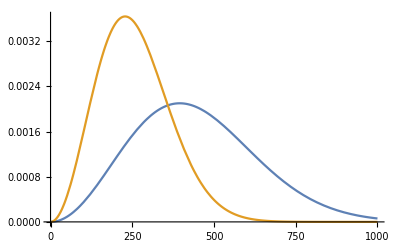

```mathematica
Plot[{f[v,28 1.66 10^-27,-10+273],f[v,84 1.66 10^-27,-10+273]},{v,0,1000}]
```

```mathematica
1.25 10^-6 xyz*(∫_300^301 f[v,84 1.66 10^-27,-10+273]ⅆv)/(∫_300^301 f[v,28 1.66 10^-27,-10+273]ⅆv)
```

2.04343×10^-6 xyz

```mathematica
1.25 10^-6 xyz*f[300.5,84 1.66 10^-27,-10+273]/f[300.5,28 1.66 10^-27,-10+273]
```

2.04343×10^-6 xyz